## Definitions

### Some parameters

```mathematica
mPlGeV=1.22*10^19;
gstarGeV=80.;
TνToTγSM=(4/11)^(1/3);
gstarToday=2+21/4 TνToTγSM^3;
Ttoday=2.73*8.62*10^-14;
TminIntegration=0.015;
GFval=1.167*10^-5.;
mWval=8.0377*10;
sWval=Sqrt[0.231];
mZval=mWval/Sqrt[1-sWval^2];
(*https://pdg.lbl.gov/2015/reviews/rpp2015-rev-astrophysical-constants.pdf, critical energy density of the Universe*)
cmMinus3toGeV3=7.692*10^-42;
h=0.673;
ρcritical=1.053*10^-5 h^2 cmMinus3toGeV3;
meVal=0.511*10^-3;
mμVal=0.105;
mτVal=1.77;
```

### Simplified Hubble factor and dt/dT, and entropy density

```mathematica
HvallGeV[T_]=√((8Pi)/3)1/mPlGeV √(Pi^2/30*gstarGeV*T^4);
tTsol[T_]=Refine[t/.Solve[HvallGeV[T]==1/(2t),t][[1]],T>0];
dtdTanalytic[T_]=D[tTsol[T],T];
(*https://pdg.lbl.gov/2012/reviews/rpp2012-rev-bbang-cosmology.pdf, eq. (21.49)*)
sT[gstar_,T_]=2 Pi^2/45*gstar*T^3;
sTtoday=sT[gstarToday,Ttoday];
```

### Neutrino chemical potential, distributions, energy densities, and asymmetries

```mathematica
(*Neutrino-antineutrino+lepton asymmetry in terms of Δn/s==L and s*)
Δnlνα[Lα_,gstar_,T_]=Lα*sT[gstar,T];
(*Eq. (5) of https://arxiv.org/pdf/2405.06509*)
Δnναμ[μ_,T_]=(μ*T^2)/6+μ^3/(6 Pi^2);
Δneμ[μ_,T_]=2*Δnναμ[μ,T];
μLα[T_,Lα_,gstar_]=μ/.Solve[Δnναμ[μ,T]==Δnlνα[Lα,gstar,T],μ][[1]];
fναFDμ[p_,T_,μνα_]=1/(Exp[p/T-μνα/T]+1);
fναFDL[p_,T_,Lα_,gstar_]=1/(Exp[p/T-μLα[T,Lα,gstar]/T]+1);
ρναtotμ[T_,μ_]=(4Pi)/(2Pi)^3*Integrate[p^3(fναFDμ[p,T,μν]+fναFDμ[p,T,-μν]),{p,0,Infinity},Assumptions->T>0&&μ>0]//Simplify;
ρναtotμ[T_,μν_]=Refine[Developer`PolyLogSimplify[ρναtotμ[T,μν]],μν>0&&T>0]//Expand//Simplify
ρναtotL[T_,Lνα_,gstar_]=ρναtotμ[T,μLα[T,Lνα,gstar]];
ρναtotZeroμ[T_]=(4Pi)/(2Pi)^3*Integrate[p^3(1/(Exp[p/T]+1)+1/(Exp[p/T]+1)),{p,0,Infinity},Assumptions->T>0&&μ>0]//Simplify;
ρlαtotμTemp[T_,m_,μ_]:=2*(4Pi)/(2Pi)^3*NIntegrate[Exp[3p] √(Exp[2p]+m^2)(fναFDμ[√(Exp[2p]+m^2),T,μ]+fναFDμ[√(Exp[2p]+m^2),T,-μ]),{p,-5,Log[30*T]}]//Simplify;
ρepem[T_,μe_]=2*ρναtotμ[T,μe];
Δnlαμ[μ_,T_,m_]:=2*(4Pi)/(2Pi)^3 NIntegrate[Exp[3p](fναFDμ[√(Exp[2p]+m^2),T,μ]-fναFDμ[√(Exp[2p]+m^2),T,-μ]),{p,-5,Log[30*T]}]
Tvs=Table[10^x,{x,Log10[TminIntegration],Log10[Tmax],(Log10[Tmax]-Log10[TminIntegration])/100}];
{ρeSM[T_],ρμSM[T_],ρτSM[T_]}=T^4*Table[Interpolation[({#,ρlαtotμTemp[#,m,0.]/#^4}&/@Tvs)//Log,InterpolationOrder->1][Log[T]]//Exp,{m,{meVal,mμVal,mτVal}}];
(*(ρναtotL[T,Lα,gstar]/.{gstar->10,Lα->0.1,T->0.025})/(ρναtotL[T,Lα,gstar]/.{gstar->10,Lα->0.,T->0.025})
ρναtotZeroμ[T]/(ρναtotL[T,Lα,gstar]/.{gstar->10,Lα->0.})/.{T->0.025}*)
```

(7 π^2 T^4)/120+(T^2 μν^2)/4+μν^4/(8 π^2)

2.89405

1.

### Zero-μ thermodynamics

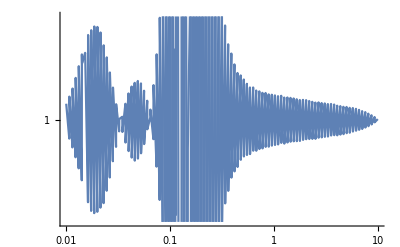

```mathematica
{Letest,Lμtest,Lτtest}={0.,0.,0.};
data=Reverse[ThermodynamicsAndAsymmetriesTotal[10.,Tmax*10^3,Letest,Lμtest,Lτtest]];
Tvals=data[[All,1]];
{HintSM[T_],gsintSM[T_],ρintSM[T_],pintSM[T_],sintSM[T_],dtdTintSM1[T_]}=Table[If[n==-1,-1,1]*(Interpolation[{Log[#[[1]]],Log[If[n==-1,-1,1]*#[[n]]]}&/@data,InterpolationOrder->1][Log[T]]//Exp),{n,{2,3,4,5,6,-1}}];

dtdTintSM[T_]=-D[ρintSM[T],T]/(3*HintSM[T]*(ρintSM[T]+pintSM[T]));
LogLogPlot[{dtdTintSM[T]/dtdTintSM1[T]},{T,0.01,10}]
aFsolSM[T_]=aF[T]/.NDSolve[{D[aF[T],T]==dtdTintSM[T]*aF[T]*HintSM[T],aF[10.]==1.},{aF[T]},{T,0.015,10.},MaxSteps->200000,(*,StartingStepSize->10^-8,Method->{"EquationSimplification"->"Solve"}*)Method->{"BDF","MaxDifferenceOrder"->2}][[1]];
```